```mathematica
ClearAll[x,y,z,u,v,w,ν,El,FI,a]
u=-FI/El ν x y z;
v=FI/El(ν/2 (x^2-y^2)z-1/6 z^3);
w=FI/El(1/2 y(ν x^2+z^2)+1/6ν y^3+(1+ν)(b^2 y-1/3y^2)-1/3a^2 ν y);
eps11=D[u,x];
eps22=D[v,y];
eps33=D[w,z];
sig1=El/((1+ν)(1-2ν))((1-ν)eps11+ν (eps22+eps33))//Simplify
sig2=El/((1+ν)(1-2ν))((1-ν)eps22+ν(eps11+eps33))//Simplify
sig3=El/((1+ν)(1-2ν))((1-ν)eps33+ν(eps11+eps22))//Simplify
sig12=El/(2(1+ν))(D[u,y]+D[v,x])
sig13=El/(2(1+ν))(D[u,z]+D[w,x])
sig23=El/(2(1+ν))(D[v,z]+D[w,y])//Simplify
```

0

0

FI y z

0

0

(FI (-(a^2-3 x^2) ν+3 b^2 (1+ν)-2 y (1+ν)))/(6 (1+ν))

```mathematica
D[sig1,x]+D[sig12,y]+D[sig13,z]
D[sig12,x]+D[sig2,y]+D[sig23,z]//Simplify
D[sig13,x]+D[sig23,y]+D[sig3,z]//Simplify
```

0

0

FI (-1/3+y)

```mathematica
{sig1,sig12,sig13}/.{x->a}//Simplify
{sig2,sig12,sig23}/.{y->b}//Simplify
{sig3,sig13,sig23}/.{z->L}//Simplify
```

{0,0,0}

{0,0,-(FI (a^2-3 x^2) ν)/(6 (1+ν))}

{FI L y,0,(FI (-(a^2-3 x^2) ν+3 b^2 (1+ν)-3 y^2 (1+ν)))/(6 (1+ν))}

```mathematica
xval={x->-0.45309,y->-0.5,z->0.046910077}
u/.ν->0/.xval/.FI->1/.El->1
v/.ν->0/.xval/.FI->1/.El->1
w/.ν->0/.xval/.FI->1/.El->1/.b->0.5
```

{x→-0.45309,y→-0.5,z→0.0469101}

0

-0.0000172047

-0.208883

```mathematica
w/.ν->0
```

(FI (b^2 y-y^3/3+(y z^2)/2))/El

```mathematica
D[w,y]/.ν->0
D[v,z]/.ν->0
```

(FI (b^2-y^2+z^2/2))/El

-(FI z^2)/(2 El)

```mathematica
s33=FI x2 x3
s31[NMax_] := FI 2 a^2/(Pi^2)ν/(1+ν)Sum[(-1)^n/n^2 Sin[n Pi x1/a]Sinh[n Pi x2/a]/Cosh[n Pi b/a],{n,1,NMax}]
s32[NMax_]:=FI (b^2-x2^2)/2 +FI ν/(1+ν)((3x1^2-a^2)/6 -2a^2/Pi^2 Sum[(-1)^n/n^2 Cos[n Pi x1/a]Cosh[n Pi x2/a]/Cosh[n Pi b/a],{n,1,NMax}])
```

FI x2 x3

```mathematica
s31[5]
s32[5]
```

1/(π^2 (1+ν))2 a^2 FI ν (-Sech[(b π)/a] Sin[(π x1)/a] Sinh[(π x2)/a]+1/4 Sech[(2 b π)/a] Sin[(2 π x1)/a] Sinh[(2 π x2)/a]-1/9 Sech[(3 b π)/a] Sin[(3 π x1)/a] Sinh[(3 π x2)/a]+1/16 Sech[(4 b π)/a] Sin[(4 π x1)/a] Sinh[(4 π x2)/a]-1/25 Sech[(5 b π)/a] Sin[(5 π x1)/a] Sinh[(5 π x2)/a])

1/2 FI (b^2-x2^2)+1/(1+ν)FI ν (1/6 (-a^2+3 x1^2)+Cos[(π x1)/a] Cosh[(π x2)/a] Sech[(b π)/a]-1/4 Cos[(2 π x1)/a] Cosh[(2 π x2)/a] Sech[(2 b π)/a]+1/9 Cos[(3 π x1)/a] Cosh[(3 π x2)/a] Sech[(3 b π)/a]-1/16 Cos[(4 π x1)/a] Cosh[(4 π x2)/a] Sech[(4 b π)/a]+1/25 Cos[(5 π x1)/a] Cosh[(5 π x2)/a] Sech[(5 b π)/a])

```mathematica
aexp=D[s31[5],x1]+D[s32[5],x2]+D[s33,x3]//Simplify
```

0

```mathematica
s31[5]/.{x1->-a}//Simplify
s31[5]/.{x1->a}//Simplify
```

0

0

```mathematica
s32[5]/.{x2->b}//Simplify
s32[5]/.{x2->b}//Simplify
```

(FI ν (1/6 (-a^2+3 x1^2)-(2 a^2 (-Cos[(π x1)/a]+1/4 Cos[(2 π x1)/a]-1/9 Cos[(3 π x1)/a]+1/16 Cos[(4 π x1)/a]-1/25 Cos[(5 π x1)/a]))/π^2))/(1+ν)

(FI ν (1/6 (-a^2+3 x1^2)-(2 a^2 (-Cos[(π x1)/a]+1/4 Cos[(2 π x1)/a]-1/9 Cos[(3 π x1)/a]+1/16 Cos[(4 π x1)/a]-1/25 Cos[(5 π x1)/a]))/π^2))/(1+ν)

```mathematica
aexp=D[s31[50],x1]+D[s32[50],x2]+D[s33,x3]//Simplify
```

0

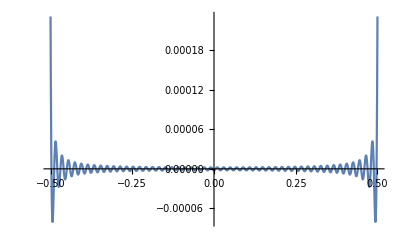

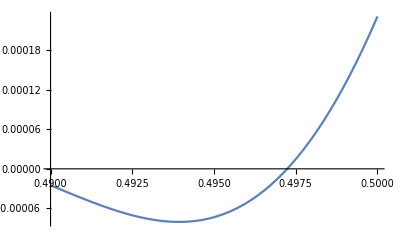

```mathematica
Plot[s32[50]/.config/.{x2->b}/.config,{x1,-1/2,1/2},PlotRange->All]
Plot[s32[50]/.config/.{x2->b}/.config,{x1,1/2-1/100,1/2},PlotRange->All]
```